# Lab #5

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Initial Equation

```mathematica
f = x''[t]==x[t]^2-x[t]
```

x''[t]==-x[t]+x[t]^2

Trying to solve analytically

```mathematica
DSolve[{f,x[0]==0,x'[0]==0},x[t],t]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

Graph with initial condition of x[0]=0

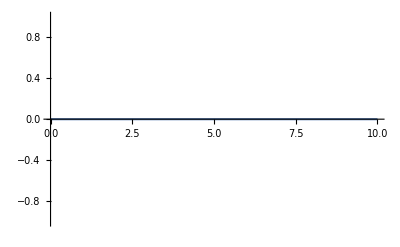

```mathematica
sol = NDSolve[{f,x[0]==0,x'[0]==0},x[t],{t,0,10}];
initialZero = x[t] /.sol;
Plot[initialZero,{t,0,10}]
```

Graph with initial condition of x[0]=.1 and x[0]=-.1

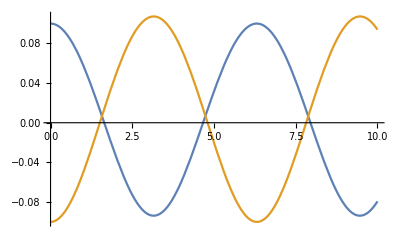

```mathematica
sol= NDSolve[{f,x[0]==0.1,x'[0]==0},x[t],{t,0,10}];
smallPositiveInitial = x[t] /.sol;
sol= NDSolve[{f,x[0]==-0.1,x'[0]==0},x[t],{t,0,10}];
smallNegativeInitial = x[t]/.sol;
Plot[{smallPositiveInitial,smallNegativeInitial},{t,0,10}]
```

Graph with initial condition of x[0]=.5 and x[0]=-.5

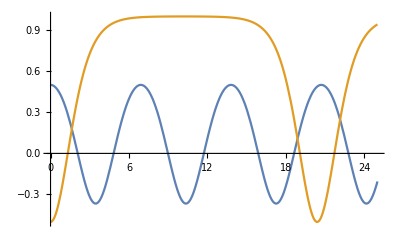

```mathematica
sol= NDSolve[{f,x[0]==0.5,x'[0]==0},x,{t,0,25}];
mediumPositiveInitial = x [t]/.sol;
sol= NDSolve[{f,x[0]==-0.5,x'[0]==0},x,{t,0,25}];
mediumNegativeInitial = x[t]/.sol;
Plot[{mediumPositiveInitial,mediumNegativeInitial},{t,0,25}]
```

Graph with initial condition of x[0]=-.51

NDSolve::ndsz: At t == 9.13172, step size is effectively zero; singularity or stiff system suspected.

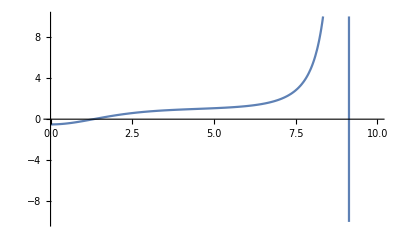

```mathematica
sol= NDSolve[{f,x[0]==-0.51,x'[0]==0},x[t],{t,0,10}];
highestPositiveInitial = x [t]/.sol;
Plot[highestPositiveInitial,{t,0,10},PlotRange->{-10,10}]
```

Potential Energy Function

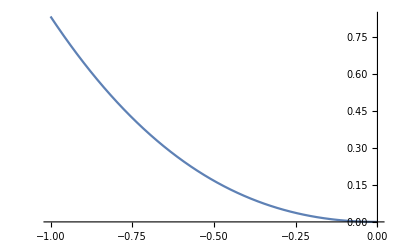

```mathematica
Vx=-Integrate[x^2-x,x];
Plot[Vx,{x,-1,0}]
```

The equation oscillates when its initial position is not 0 but greater than -0.5 or less than 0.5. Below -0.51 the x squared term overpowers the x term and you get an exponential growth of power. This is corroborated by the energy graph which shows an inflection point at -0.5 after which the energy grows exponentially.